## Order dependent protection and immunity gaps

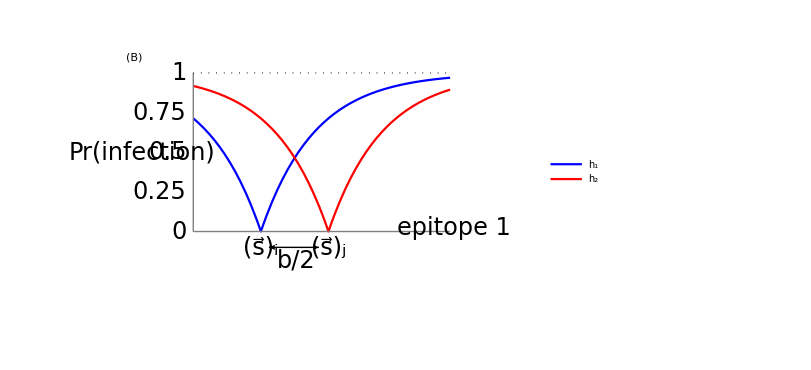

```mathematica
h1timeline = Show[
Graphics[Style[Text["(A)",{-0.3,.8}],FontSize->24]],
Graphics[{Arrowheads[{0,0.02}],Arrow[{{0,0},{4,0}}]}],
Graphics[{Black, Rectangle[{1-.1,-.1},{1+0.1,0.1}]}],
Graphics[{Black,Triangle[{{2.5-.1,-0.1},{2.5+0.1,-0.1},{2.5,.1}}]}],
Graphics[Style[Text["h_1",{-0.1,0.05}],FontSize->24]],
Graphics[Style[Text[Subscript[OverVector[s], i],{1,0.3}],FontSize->24]],
Graphics[Style[Text[Subscript[OverVector[s], j],{2.5,0.3}],FontSize->24]],
Graphics[Style[Text["time",{4.25,0}],FontSize->24]]
];
h2timeline=Show[
Graphics[Style[Text["",{-0.3,0.7}],FontSize->24]],
Graphics[{Arrowheads[{0,0.02}],Arrow[{{0,0},{4,0}}]}],
Graphics[{Black,Triangle[{{1-.1,-0.1},{1+0.1,-0.1},{1,.1}}]}],
Graphics[{Black, Rectangle[{2.5-.1,-.1},{2.5+0.1,0.1}]}],
Graphics[Style[Text["h_2",{-0.1,0.05}],FontSize->24]],
Graphics[Style[Text[Subscript[OverVector[s], j],{1,0.3}],FontSize->24]],
Graphics[Style[Text[Subscript[OverVector[s], i],{2.5,0.3}],FontSize->24]],
Graphics[Style[Text["time",{4.25,0}],FontSize->24]]
];

orderdepplotall = Plot[{1-Exp[-Abs[x]/.4],1-Exp[-Abs[x-.5]/.4]}, {x,-0.5,1.4}, 
PlotRange->{{-1,2},{-0.5,1.25}},
PlotStyle->{Blue,Red},
AxesLabel->{Style["antigenic space coord",24,Black],Style["Pr(infection)",24,Black]},
Axes->{False,False},
PlotLegends->Placed[{Style["h_1",24],Style["h_2",24],Black},{Right,Center}],
Ticks->{False,{0.25,0.5,0.75,1}}, 
TicksStyle->{Black,24},  
ImageSize->600];
s1label = Graphics[Text[Style["(s⃗)_i",FontSize->24],{0,-0.1}]];
s2label = Graphics[Text[Style["(s⃗)_j",FontSize->24],{0.5,-0.1}]];
underarrow = Graphics[{Arrowheads[{-.02,0.02}],Arrow[{{0.06,-0.1},{0.43,-0.1}}]}];
arrowlabel = Graphics[Text[Style["b/2",24,Black],{0.261,-0.18}]];
xaxis = Graphics[{Gray,Line[{{-0.5,0},{1.4,0}}]}];
xaxislabel = Graphics[Text[Style["epitope 1",FontSize->24],{1.85,0.02},Right,Background->White]];
yaxis = Graphics[{Gray, Line[{{-0.5,1},{-0.5,0}}]}];
yaxislabel =Graphics[ Rotate[Text[Style["Pr(infection)",FontSize->24],{-.88,0.5}],Pi/2]];
pr1line = Graphics[{Black, Dotted,Thick, Line[{{-0.5,1},{1.4,1}}]}];
yaxistick1 = Graphics[Text[Style["0",FontSize->24],{-.55,0},Right]];
yaxistick2 = Graphics[Text[Style["0.25",FontSize->24],{-.55,0.25},Right]];
yaxistick3 = Graphics[Text[Style["0.5",FontSize->24],{-.55,0.5},Right]];
yaxistick4 = Graphics[Text[Style["0.75",FontSize->24],{-.55,0.75},Right]];
yaxistick5 = Graphics[Text[Style["1",FontSize->24],{-.55,1},Right]];
totalaxis = Show[xaxis, xaxislabel,yaxis,yaxislabel,yaxistick1,yaxistick2,yaxistick3,yaxistick4,yaxistick5,pr1line,underarrow,arrowlabel];
hostmemplot = Show[{orderdepplotall, s1label, s2label},ImagePadding->{{21, Automatic}, {Automatic, Automatic}}];
hostmemplotpanel=Show[{hostmemplot,totalaxis,Graphics[Style[Text["(B)",{-1,1.1},Left],FontSize->24]]}, ImageSize->600, ImagePadding->{{21, Automatic}, {Automatic, Automatic}}];
timelines = GraphicsColumn[{h1timeline,h2timeline},Spacings->-10,ImageSize->500, ImagePadding->{{Automatic, Automatic}, {150, -20}}];
finishedfig=GraphicsRow[{timelines,hostmemplotpanel},ImageSize->1500]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["../figures/order_dependence.pdf",finishedfig]
```

../figures/order_dependence.pdf